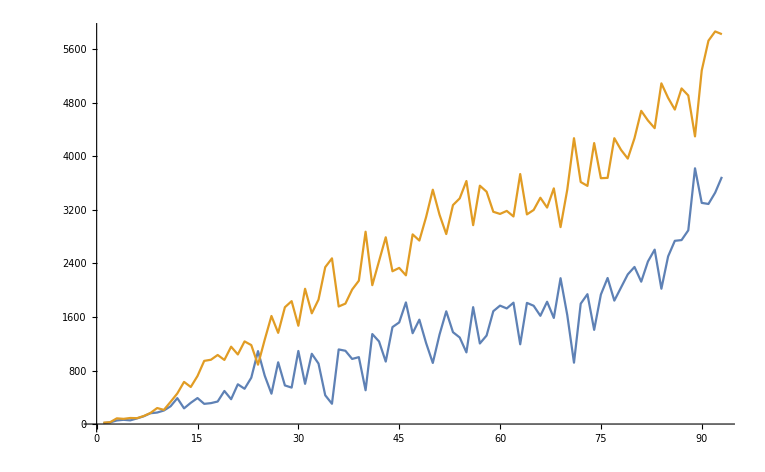

```mathematica
Show[ListLinePlot[Transpose@(SortBy[#,Mean]&@Table[
{QuantityMagnitude[ElementData[i,"MeltingPoint"],"K"],
QuantityMagnitude[ElementData[i,"BoilingPoint"],"K"]},
{i,1,118}])[[;;93]]],Plot[None,{x,0,4000}]]
```

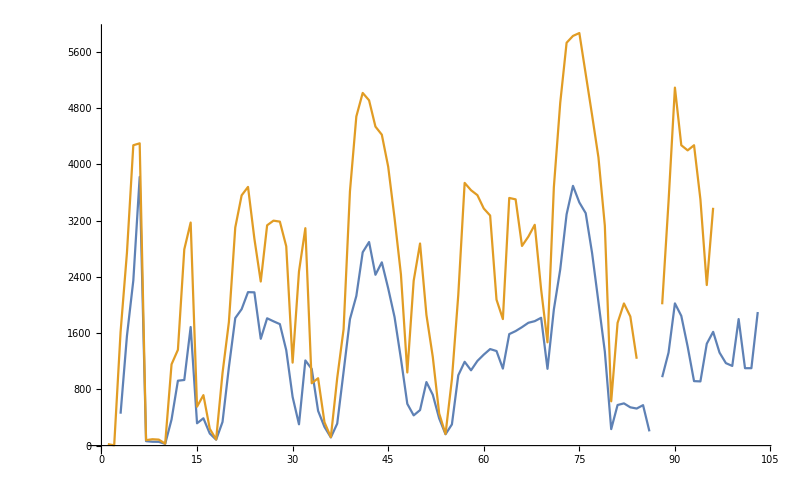

```mathematica
Show[ListLinePlot[Transpose@Table[
{QuantityMagnitude[ElementData[i,"MeltingPoint"],"K"],
QuantityMagnitude[ElementData[i,"BoilingPoint"],"K"]},
{i,1,118}]],Plot[None,{x,0,4000}]]
```

```mathematica
MaximalBy[#,If[NumberQ[#],#,0]&@#[[2]]&]&@Table[
{i,QuantityMagnitude[ElementData[i,"MeltingPoint"],"K"]-
QuantityMagnitude[ElementData[i,"BoilingPoint"],"K"]},
{i,1,118}]
```

{{33,200.}}

```mathematica
ElementData[33,"MeltingPoint"]
ElementData[33,"BoilingPoint"]
```

817. °C

614. °C

```mathematica
mbs=Table[
{QuantityMagnitude[ElementData[i,"MeltingPoint"],"K"],
QuantityMagnitude[ElementData[i,"BoilingPoint"],"K"]},
{i,1,118}];
ms=Select[Table[
QuantityMagnitude[ElementData[i,"MeltingPoint"],"K"],
{i,1,118}],NumberQ];
bs=Select[Table[
QuantityMagnitude[ElementData[i,"BoilingPoint"],"K"],
{i,1,118}],NumberQ];
```

```mathematica
ngas[t_]:=Length[Select[Range[118],
mbs[[#,2]]<t&]]
nsol[t_]:=Length[Select[Range[118],
mbs[[#,1]]>t&]]
nliq[t_]:=Length[Select[Range[118],
mbs[[#,1]]<t&&mbs[[#,2]]>t&]]
```

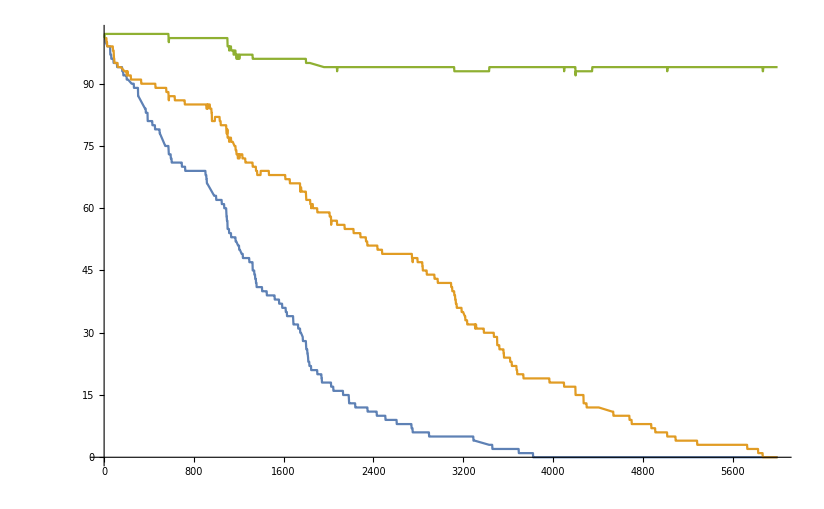

```mathematica
Plot[{nsol[t],nsol[t]+nliq[t],nsol[t]+nliq[t]+ngas[t]},{t,0,6000}]
```

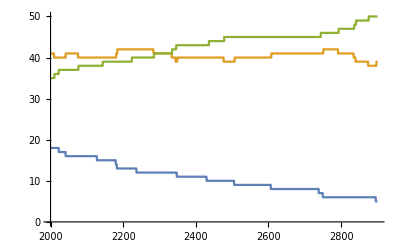

```mathematica
Plot[{nsol[t],nliq[t],ngas[t]},{t,2000,2900}]
```

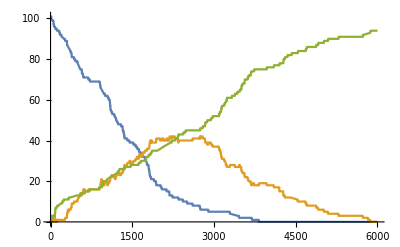

```mathematica
Plot[{nsol[t],nliq[t],ngas[t]},{t,0,6000}]
```

```mathematica
nliq[2200]
```

42

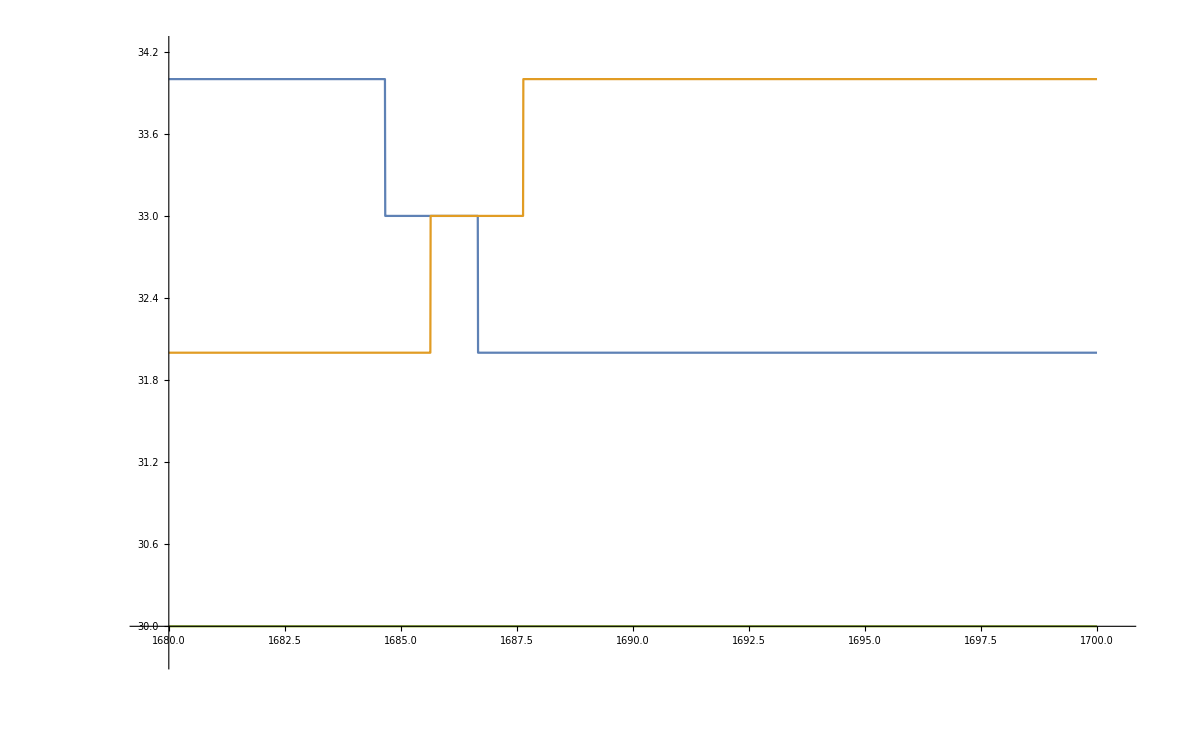

```mathematica
Plot[{nsol[t],nliq[t],ngas[t]},{t,1680,1700}]
```